```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\VS_workspace\CPlusPlus\SOHR\projects\catalytic_cycle\theory\wall_S_chattering_problem

## A⇌_k2^k1 B⟶^k3 C problem

### Solve differential equation like d[A]/dt=-k1[A]+k2[B] d[B]/dt=k1[A]-k2[B]-k3[B] d[C]/dt=k3[B]

```mathematica
(*left hand side of equation in terms of k1, k2, k3 and t*)
Clear[LHS];LHS[k1_,k2_,t_,k3_]:=
Module[{soln,output,x1,x2,x3},
soln=DSolve[{x1'[t]==-k1 *x1 [t] + k2 *x2[t],x2'[t]==k1*x1[t] - (k2 +k3)* x2[t],x3'[t]==k3 * x2[t], x1[0]==0, x2[0]==1.0, x3[0]==0},{x1[t],x2[t], x3[t]},t ];
output=Simplify[x3[t]/.soln[[1,3]],Assumptions->{k1>0,k2>0,k3>0,t>0}];
Return[output];]
(*left hand side of equation in terms of λ1, λ2, k3 and λ3, where λ1=k3/k1, λ2=k3/k2, λ3=k3*t*)
Clear[LHSLambda];LHSLambda[λ1_,λ2_,λ3_,k3_]:=
Module[{soln,o1,o2,x1,x2,x3,k1,k2,t},
soln=DSolve[{x1'[t]==-k1 *x1 [t] + k2 *x2[t],x2'[t]==k1*x1[t] - (k2 +k3) * x2[t],x3'[t]==k3 * x2[t], x1[0]==0, x2[0]==1.0, x3[0]==0},{x1[t],x2[t], x3[t]},t ];
o1=Simplify[x3[t]/.soln[[1,3]],Assumptions->{k1>0,k2>0,k3>0,t>0}];
o2 = Simplify[o1/.{k1->k3/λ1,k2->k3/λ2, t->λ3/k3},Assumptions->{k1>0,k2>0,k3>0,t>0}];
Return[o2];]
(*Effective K*)
Clear[EffK];EffK[k1_,k2_,t_,k3_]:=
Module[{soln,o1,o2,x1,x2,x3},
soln=DSolve[{x1'[t]==-k1 *x1 [t] + k2 *x2[t],x2'[t]==k1*x1[t] -(k2 +k3)* x2[t],x3'[t]==k3 * x2[t], x1[0]==0, x2[0]==1.0, x3[0]==0},{x1[t],x2[t], x3[t]},t ];
o1=Simplify[x3[t]/.soln[[1,3]],Assumptions->{k1>0,k2>0,k3>0,t>0}];
o2=Simplify[Log[o1]/(-(t)), Assumptions->{k1>0,k2>0,k3>0,t>0}];
Return[o2];]
(*Effective K in terms of lambda*)
Clear[EffKLambda];EffKLambda[λ1_,λ2_,λ3_,k3_]:=
Module[{soln,o1,o2,o3,x1,x2,x3,k1,k2,t},
soln=DSolve[{x1'[t]==-k1 *x1 [t] + k2 *x2[t],x2'[t]==k1*x1[t] -(k2 +k3) * x2[t],x3'[t]==k3 * x2[t], x1[0]==0, x2[0]==1.0, x3[0]==0},{x1[t],x2[t], x3[t]},t ];
o1=Simplify[x3[t]/.soln[[1,3]],Assumptions->{k1>0,k2>0,k3>0,t>0}];
o2 = Simplify[o1/.{k1->k3/λ1,k2->k3/λ2, t->λ3/k3},Assumptions->{k1>0,k2>0,k3>0,t>0}];
o3=Simplify[Log[o2]/(-(λ3/k3)), Assumptions->{λ1>0,λ2>0,k3>0,λ3>0}];
Return[o3];]
(*LHS2=Simplify[LHS/.{√(k1^2+4 k1 k2-2 k1 k3+k3^2)->Δ},Assumptions->{k1>0,k2>0,k3>0,t>0}]*)
```

```mathematica
f=LHS[k1,k2,t,k3]/.{√(-4 k1 k3+(k1+k2+k3)^2)->Δ}
```

1/(1. k1^2+2. k1 k2+1. k2^2-2. k1 k3+2. k2 k3+1. k3^2)1. ⅇ^(-1/2 t (k1+k2+k3+Δ)) (-0.5 k1^2-0.5 ⅇ^(t Δ) k1^2+1. ⅇ^(1/2 t (k1+k2+k3+Δ)) k1^2-1. k1 k2-1. ⅇ^(t Δ) k1 k2+2. ⅇ^(1/2 t (k1+k2+k3+Δ)) k1 k2-0.5 k2^2-0.5 ⅇ^(t Δ) k2^2+1. ⅇ^(1/2 t (k1+k2+k3+Δ)) k2^2+1. k1 k3+1. ⅇ^(t Δ) k1 k3-2. ⅇ^(1/2 t (k1+k2+k3+Δ)) k1 k3-1. k2 k3-1. ⅇ^(t Δ) k2 k3+2. ⅇ^(1/2 t (k1+k2+k3+Δ)) k2 k3-0.5 k3^2-0.5 ⅇ^(t Δ) k3^2+1. ⅇ^(1/2 t (k1+k2+k3+Δ)) k3^2+0.5 k1 Δ-0.5 ⅇ^(t Δ) k1 Δ+0.5 k2 Δ-0.5 ⅇ^(t Δ) k2 Δ-0.5 k3 Δ+0.5 ⅇ^(t Δ) k3 Δ)

```mathematica
Normal[Series[Log[1-f],{t,0,2}]]/(-t)//Simplify
```

(0.5 (1. k1^2+2. k1 k2+1. k2^2-2. k1 k3+2. k2 k3+1. k3^2) (1. k1^3+1. k2^3+k1^2 (3. k2-1. k3)+3. k2^2 k3+3. k2 k3^2+1. k3^3-1. k2 Δ^2+1. k3 Δ^2+k1 (3. k2^2+2. k2 k3-1. k3^2-1. Δ^2))-0.125 t Δ^2 (1. k1^4+1. k2^4+k1^3 (4. k2-4. k3)+4. k2^3 k3+1. k3^4-1. k3^2 Δ^2+k2^2 (6. k3^2-1. Δ^2)+k1^2 (6. k2^2-4. k2 k3+6. k3^2-1. Δ^2)+k2 (4. k3^3+2. k3 Δ^2)+k1 (4. k2^3+4. k2^2 k3-4. k2 k3^2-4. k3^3-2. k2 Δ^2+2. k3 Δ^2)))/(1. k1^2+2. k1 k2+1. k2^2-2. k1 k3+2. k2 k3+1. k3^2)^2

```mathematica
Clear[λ1,λ2,λ3,k3];Normal[Series[Log[1-LHSLambda[λ1,λ2,λ3,k3]],{λ3,0,2}]]//Simplify;
```

```mathematica
Clear[k1,k2,t,k3];Normal[Series[Log[1-LHS[k1,k2,t,k3]],{t,0,2}]]//Simplify
```

(k3 t (-1. k3^4+0.5 k2^5 t+k1^4 (-1.+0.5 k2 t)+k2 k3^3 (-4.+0.5 k3 t)+k2^2 k3^2 (-6.+2. k3 t)+k2^4 (-1.+2. k3 t)+k2^3 k3 (-4.+3. k3 t)+k1^3 (4. k3+2. k2^2 t+k2 (-4.-2. k3 t))+k1 (4. k3^3+2. k2^4 t+k2^2 k3 (-4.-2. k3 t)+k2 k3^2 (4.-2. k3 t)+k2^3 (-4.+2. k3 t))+k1^2 (-6. k3^2+3. k2^3 t+k2^2 (-6.-2. k3 t)+k2 k3 (4.+3. k3 t))))/(1. k1^2+2. k1 k2+1. k2^2-2. k1 k3+2. k2 k3+1. k3^2)^2

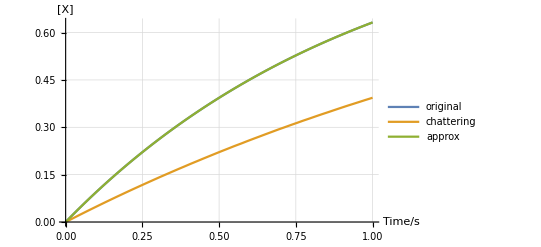

```mathematica
Plot[{1-ⅇ^(-k4*t)/.{k4->10^13,k1->10^25,k2->10^25},LHS[k1,k2,t,k3]/.{k1->10^25,k2->10^25,k3->10^13}//Evaluate,1-ⅇ^(-(k4)*t)/.{k4->10^13,k1->10^25,k2->10^25}},{t,0, 10^-13},PlotLegends->{"original","chattering","approx"},GridLines->Automatic,AxesLabel->{"Time/s","[X]"}]
```

```mathematica
LHS[k1,k2,t,k3]
```

1/(1. k1^2+2. k1 k2+1. k2^2-2. k1 k3+2. k2 k3+1. k3^2)1. ⅇ^(-1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) (-0.5 k1^2-0.5 ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k1^2+1. ⅇ^(1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) k1^2-1. k1 k2-1. ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k1 k2+2. ⅇ^(1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) k1 k2-0.5 k2^2-0.5 ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k2^2+1. ⅇ^(1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) k2^2+1. k1 k3+1. ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k1 k3-2. ⅇ^(1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) k1 k3-1. k2 k3-1. ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k2 k3+2. ⅇ^(1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) k2 k3-0.5 k3^2-0.5 ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k3^2+1. ⅇ^(1/2 (k1+k2+k3+√(-4 k1 k3+(k1+k2+k3)^2)) t) k3^2+0.5 k1 √(-4 k1 k3+(k1+k2+k3)^2)-0.5 ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k1 √(-4 k1 k3+(k1+k2+k3)^2)+0.5 k2 √(-4 k1 k3+(k1+k2+k3)^2)-0.5 ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k2 √(-4 k1 k3+(k1+k2+k3)^2)-0.5 k3 √(-4 k1 k3+(k1+k2+k3)^2)+0.5 ⅇ^(√(-4 k1 k3+(k1+k2+k3)^2) t) k3 √(-4 k1 k3+(k1+k2+k3)^2))

```mathematica
LHSLambda[λ1,λ2,λ3,k3]
```

-1/(λ1 (2.-2. λ2) λ2+1. λ2^2+1. λ1^2 (1.+1. λ2)^2)0.5 ⅇ^(-((λ1+λ2+λ1 λ2+λ1 √(-4/λ1+(1+1/λ1+1/λ2)^2) λ2) λ3)/(2 λ1 λ2)) ((1.+1. ⅇ^(√(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2) λ3)-2. ⅇ^(((λ1+λ2+λ1 λ2+λ1 λ2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)) λ3)/(2 λ1 λ2))) λ2^2+1. λ1 λ2 (2.-2. λ2+ⅇ^(((λ1+λ2+λ1 λ2+λ1 λ2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)) λ3)/(2 λ1 λ2)) (-4.+4. λ2)-1. λ2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)+1. ⅇ^(√(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2) λ3) (2.-2. λ2+1. λ2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)))-1. λ1^2 (-1.-2. λ2-1. λ2^2+2. ⅇ^(((λ2+λ1 (1+λ2+λ2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2))) λ3)/(2 λ1 λ2)) (1.+1. λ2)^2+1. λ2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)-1. λ2^2 √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)+1. ⅇ^(√(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2) λ3) (-1.+λ2 (-2.-1. √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2))+λ2^2 (-1.+1. √(1/λ1^2+(-2+2/λ2)/λ1+(1+λ2)^2/λ2^2)))))